# Leading order cross section for qq̄→(χ̃)_i^0(χ̃)_j^0

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Leading order cross section of neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`
<< CalcTools`
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

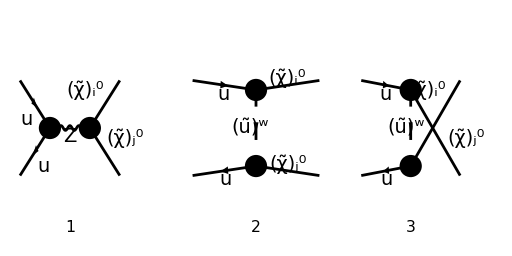

```mathematica
treeDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2, ExcludeTopologies -> {Boxes,SelfEnergies,Tadpoles}], 
	{F[3, {1, a}], -F[3, {1, b}]} -> {F[11, {i}], F[11, {j}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling,NoElectronHCoupling},
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ColumnsXRows -> {3, 1}, ImageSize->{512,256}];
```

```mathematica
M0[0] = FCFAConvert[
	CreateFeynAmp[treeDiagrams], 
	IncomingMomenta -> {ki,kj},
	OutgoingMomenta -> {pi,pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν},
	FinalSubstitutions -> AmpSimplifyRules
]/.{IndexDelta -> FeynCalc`IndexDelta};
```

```mathematica
tempPrefactor = SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
M0[1] = tempPrefactor*DiracSimplify/@(Convert2QZCharges/@(M0[0]/tempPrefactor));
M0[2] = M0[1]/.{Opp[i_,j_,L]*->-Opp[i,j,R]}//.SuperChargeRules;
Clear[tempPrefactor]
```

Divide the three amplitudes into separate channels and convert to Q_A^XY and Z_s^X supercharges.

```mathematica
Ms[0] = (Part[M0[0],1]/.ZSimplifyRules//FeynAmpDenominatorExplicit)/.SMP["m_Z"]^2->DZ
Mt[0] = FeynAmpDenominatorExplicit[Part[M0[0],2]//.QSimplifyRules]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->A
Mu[0] = FeynAmpDenominatorExplicit[Part[M0[0],3]//.QSimplifyRules]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->A

MsC[0] = ConjugateAmplitude[Ms[0]]/.{A->B,μ->ρ,ν->σ};
MtC[0] = ConjugateAmplitude[Mt[0]]/.{A->B,μ->ρ,ν->σ};
MuC[0] = ConjugateAmplitude[Mu[0]]/.{A->B,μ->ρ,ν->σ};
```

-(g^μν (φ(-k_j)).(-ⅈ g_W γ^μ.(γ̄)^7 δ_ab C_qqZ^L-ⅈ g_W γ^μ.(γ̄)^6 δ_ab C_qqZ^R).(φ(k_i)) (φ(p_j,m_j)).(-ⅈ g_W γ^ν.(γ̄)^6 O_ij^(′′L)-ⅈ g_W γ^ν.(γ̄)^7 O_ij^(′′R)).(φ(-p_i,m_i)))/(s-Δ_Z)

((φ(-k_j)).(-ⅈ √2 (γ̄)^6 g_W δ_ab C_(u(ũ)_A(χ̃)_j^0)^L-ⅈ √2 (γ̄)^7 g_W δ_ab C_(u(ũ)_A(χ̃)_j^0)^R).(φ(-p_j,m_j)) (φ(p_i,m_i)).(-(ⅈ (γ̄)^7 g_W (m_W s_β (6 (cos(θ_W)) Conjugate[(C_(u(ũ)_A(χ̃)_i^0)^L)]-R_A1^((ũ)_1) (sin(θ_W)) Conjugate[(N_(i,1))])+m_W s_β R_A1^((ũ)_1) (sin(θ_W)) Conjugate[(N_(i,1))]))/(3 √2 m_W s_β (cos(θ_W)))-ⅈ √2 (γ̄)^6 g_W Conjugate[(C_(u(ũ)_A(χ̃)_i^0)^R)]).(φ(k_i)))/(t-Δ_A)

-((φ(-k_j)).(-ⅈ √2 (γ̄)^6 g_W δ_ab C_(u(ũ)_A(χ̃)_i^0)^L-ⅈ √2 (γ̄)^7 g_W δ_ab C_(u(ũ)_A(χ̃)_i^0)^R).(φ(-p_i,m_i)) (φ(p_j,m_j)).(-(ⅈ (γ̄)^7 g_W (m_W s_β (6 (cos(θ_W)) Conjugate[(C_(u(ũ)_A(χ̃)_j^0)^L)]-R_A1^((ũ)_1) (sin(θ_W)) Conjugate[(N_(j,1))])+m_W s_β R_A1^((ũ)_1) (sin(θ_W)) Conjugate[(N_(j,1))]))/(3 √2 m_W s_β (cos(θ_W)))-ⅈ √2 (γ̄)^6 g_W Conjugate[(C_(u(ũ)_A(χ̃)_j^0)^R)]).(φ(k_i)))/(u-Δ_A)

Save results in “results/LO/NNamps.m”
They can be loaded with
LOAmps=Import[FileNameJoin[{ResultsDir,"NNamps.m"}]];
which creates a list containing the s, t, u amplitudes followed by their conjugates in the same order.

```mathematica
Export[FileNameJoin[{ResultsDir, "NNamps.m"}], ToString/@FullForm/@{Ms[0],Mt[0],Mu[0],MsC[0],MtC[0],MuC[0]}];
```

## Differential Cross-Section

Some more text

```mathematica
Iss[0] = SquareAmplitudes[Ms[0],MsC[0]];
Itt[0] = SquareAmplitudes[Mt[0],MtC[0]];
Iuu[0] = SquareAmplitudes[Mu[0],MuC[0]];
Ist[0] = (SquareAmplitudes[Ms[0],MtC[0]/.B->A]+SquareAmplitudes[Mt[0],MsC[0]])/2;
Isu[0] = (SquareAmplitudes[Ms[0],MuC[0]/.B->A]+SquareAmplitudes[Mu[0],MsC[0]])/2;
Itu[0] = (SquareAmplitudes[Mt[0],MuC[0]]+SquareAmplitudes[Mu[0]/.A->B,MtC[0]/.B->A])/2;
```

Convert the dimension D→4.

```mathematica
Iss[1] = FixDimension[Iss[0]/.Convert2Den];
Itt[1] = FixDimension[Itt[0]/.Convert2Den];
Iuu[1] = FixDimension[Iuu[0]/.Convert2Den];
Ist[1] = FixDimension[Ist[0]/.Convert2Den];
Isu[1] = FixDimension[Isu[0]/.Convert2Den];
Itu[1] = FixDimension[Itu[0]/.Convert2Den];
(*Iss[1] = Iss[0]/.Convert2Den;
Itt[1] = Itt[0]/.Convert2Den;
Iuu[1] = Iuu[0]/.Convert2Den;
Ist[1] = Ist[0]/.Convert2Den;
Isu[1] = Isu[0]/.Convert2Den;
Itu[1] = Itu[0]/.Convert2Den;*)
```

Draw out common prefactor between the squared amplitudes and factor them in terms of denominators and basic kinematic terms.

```mathematica
CommonPrefactor = 4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
Iss[2] = CommonPrefactor FactorDenominators[Iss[1]/CommonPrefactor];
Itt[2] = CommonPrefactor FactorDenominators[Itt[1]/CommonPrefactor];
Iuu[2] = CommonPrefactor FactorDenominators[Iuu[1]/CommonPrefactor];
Ist[2] = CommonPrefactor FactorDenominators[Ist[1]/CommonPrefactor];
Isu[2] = CommonPrefactor FactorDenominators[Isu[1]/CommonPrefactor];
Itu[2] = CommonPrefactor FactorDenominators[Itu[1]/CommonPrefactor];
```

We can convert these to  Q_A^XY and Z_s^X supercharges, and write them out in a nice form using this.

```mathematica
CommonPrefactor Collect[
	Expand[Itt[2]/CommonPrefactor]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules,
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	FullSimplify
]
```

4 g_W^4 δ_ab^2 1/(t-Δ_A) 1/(t-Δ_B^*) (t-m_i^2) (t-m_j^2) (Q_(ũ B)^LR Conjugate[(Q_(ũA)^LR)]+Q_(ũ B)^RL Conjugate[(Q_(ũA)^RL)]+Q_(ũ B)^LL Conjugate[(Q_(ũA)^LL)]+Q_(ũ B)^RR Conjugate[(Q_(ũA)^RR)])

Add all squared amplitudes, omitting the common prefactor.

```mathematica
Itot[0] = (Iss[2]+Itt[2]+Iuu[2]+2Ist[2]+2Isu[2]+2Itu[2])/CommonPrefactor;
Itot[1] = Collect[
	Itot[0],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Collect[
		#1,
		Den[args1__]Den[args2__],
		(FullSimplify[Expand[#1]//.SuperChargeRules]&)
	]&)
];
```

Show that the total amplitude can be written as effective charges in front of four different kinematic terms.

```mathematica
Collect[
	Itot[1] // SelectFree2[#, DiracTrace]&,
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(937) s m_i m_j+Q(947) (t u-m_i^2 m_j^2)+Q(941) (t-m_i^2) (t-m_j^2)+Q(945) (u-m_i^2) (u-m_j^2)

Calculate the total differential cross section and save to “results/LO/NNdxsec.m”

```mathematica
DiffXSecPrefactor = CommonPrefactor/(64 Pi CA^2 s^2)IdenticalPartFactor[i,j] /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
DiffXSec = DiffXSecPrefactor Itot[1] /. {(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]}

Export[FileNameJoin[{ResultsDir, "NNdxsec.m"}], FullForm[DiffXSec]//ToString];
```

1/(C_A s^2)α_W^2 π (1/2)^(i,j) ((u-m_i^2) (u-m_j^2) Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 (t-m_i^2) (t-m_j^2)+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 (t-m_i^2) (t-m_j^2)+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 (u-m_i^2) (u-m_j^2)+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)] 1/(t-Δ_A) 1/(u-Δ_B^*) (t u-m_i^2 m_j^2)+1/(u-Δ_A^*) (u-m_i^2) (u-m_j^2) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)-1/(t-Δ_A^*) (t-m_i^2) (t-m_j^2) (Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR)+(u-m_i^2) (u-m_j^2) (1/(u-Δ_A) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+1/(u-Δ_A) 1/(u-Δ_B^*) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR))+1/(t-Δ_A^*) 1/(u-Δ_B) (t u-m_i^2 m_j^2) Q_(ũ A)^RL Q_(ũ B)^LR+(t u-m_i^2 m_j^2) (Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)] 1/(t-Δ_A) 1/(u-Δ_B^*)+1/(t-Δ_A^*) 1/(u-Δ_B) Q_(ũ A)^LR Q_(ũ B)^RL)+(t-m_i^2) (t-m_j^2) (1/(t-Δ_A) 1/(t-Δ_B^*) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR)-(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) 1/(t-Δ_A))+s m_i m_j (-((Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Conjugate[(Q_(ũA)^RR)]) 1/(t-Δ_A))+(-Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(ũB)^LL)]-Conjugate[(Q_(ũA)^RR)] Conjugate[(Q_(ũB)^RR)]) 1/(u-Δ_B^*) 1/(t-Δ_A)+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+1/(u-Δ_A^*) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR+1/(u-Δ_A) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Q_(ũ A)^RR)-1/(t-Δ_A^*) (Z_((χ̃)_i^0(χ̃)_j^0)^LL Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Q_(ũ A)^RR)+1/(t-Δ_A^*) 1/(u-Δ_B) (-Q_(ũ A)^LL Q_(ũ B)^LL-Q_(ũ A)^RR Q_(ũ B)^RR)))

```mathematica
DiffXSecPrefactor Collect[
	ReplaceAll[DiffXSec/DiffXSecPrefactor, {DSf[args__]->MSf[args]^2(*, DZ->SMP["m_Z"]^2*), DSfC[args__]->MSf[args]^2}],
	{s*MEW[i]*MEW[j],(t-MEW[i]^2)(t-MEW[j]^2),(u-MEW[i]^2)(u-MEW[j]^2),t*u-MEW[i]^2*MEW[j]^2},
	(Collect[
		#1,
		Den[args1__]Den[args2__],
		(FullSimplify[Expand[#1]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules]&)
	]&)
] // Refine[#, Assumptions->{SMP[_]∈Reals, MSf[__]∈Reals}]&;
% //. {a_+a_* -> 2Re[a], a_ b_+a_*b_* -> 2Re[a b], a_ b_*+a_*b_ -> 2Re[a b*], a_^2+a_*^2 -> 2Re[a^2]}
```

1/(s^2 C_A)π α_W^2 (1/2)^(i,j) ((t-m_i^2) (t-m_j^2) (-1/(t-m_((ũ)_(1,A))^2) (2 Re(Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LR)+2 Re(Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RL))+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+1/(t-m_((ũ)_(1,A))^2) 1/(t-m_((ũ)_(1,B))^2) (Q_(ũ B)^LR Conjugate[(Q_(ũA)^LR)]+Q_(ũ B)^RL Conjugate[(Q_(ũA)^RL)]+Q_(ũ B)^LL Conjugate[(Q_(ũA)^LL)]+Q_(ũ B)^RR Conjugate[(Q_(ũA)^RR)]))+(u-m_i^2) (u-m_j^2) (1/(u-m_((ũ)_(1,A))^2) (2 Re(Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL)+2 Re(Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR))+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2+1/(u-m_((ũ)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (Q_(ũ A)^LR Conjugate[(Q_(ũB)^LR)]+Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]+Q_(ũ A)^RR Conjugate[(Q_(ũB)^RR)]))+s m_i m_j (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] (Z_((χ̃)_i^0(χ̃)_j^0)^LR-1/(t-m_((ũ)_(1,A))^2) Conjugate[(Q_(ũA)^LL)])+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] (Z_((χ̃)_i^0(χ̃)_j^0)^RL-1/(t-m_((ũ)_(1,A))^2) Conjugate[(Q_(ũA)^RR)])+1/(u-m_((ũ)_(1,A))^2) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] (Z_((χ̃)_i^0(χ̃)_j^0)^LL+Q_(ũ A)^LL 1/(u-m_((ũ)_(1,A))^2))+Q_(ũ A)^RR 1/(u-m_((ũ)_(1,A))^2) Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]-1/(t-m_((ũ)_(1,A))^2) (Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LL+Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RR)+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]+1/(t-m_((ũ)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (-Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(ũB)^LL)]-Conjugate[(Q_(ũA)^RR)] Conjugate[(Q_(ũB)^RR)]-Q_(ũ A)^LL Q_(ũ B)^LL-Q_(ũ A)^RR Q_(ũ B)^RR))+1/(t-m_((ũ)_(1,A))^2) 1/(u-m_((ũ)_(1,B))^2) (t u-m_i^2 m_j^2) (2 Re(Q_(ũ A)^RL Q_(ũ B)^LR)+2 Re(Q_(ũ A)^LR Q_(ũ B)^RL)))

Printing the individual contributions to the differential cross-section.

```mathematica
ZXsecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Qtu[_][__][__] -> 0 // CollectEffCharges // FRH)
SqXSecDiff = DiffXSecPrefactor (DiffXSec/DiffXSecPrefactor /. Zij["NN"][_] -> 0 // CollectEffCharges // FRH)
InterferenceXSecDiff = DiffXSecPrefactor (DiffXSec / DiffXSecPrefactor //
	SelectNotFree2[#, Zij]& // SelectNotFree2[#, Qtu]& //
	CollectEffCharges // FRH)
```

(π α_W^2 (1/2)^(i,j) ((t-m_i^2) (t-m_j^2) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2)+(u-m_i^2) (u-m_j^2) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)+s m_i m_j (Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)])))/(s^2 C_A)

1/(C_A s^2)α_W^2 π (1/2)^(i,j) (-s (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Conjugate[(Q_(ũA)^RR)]) 1/(t-Δ_A) m_i m_j-s (Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(ũB)^LL)]+Conjugate[(Q_(ũA)^RR)] Conjugate[(Q_(ũB)^RR)]) 1/(t-Δ_A) 1/(u-Δ_B^*) m_i m_j+s 1/(u-Δ_A^*) m_i (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL) m_j+s m_i (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) m_j+s 1/(u-Δ_A) m_i (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Q_(ũ A)^RR) m_j-s 1/(t-Δ_A^*) m_i (Z_((χ̃)_i^0(χ̃)_j^0)^LL Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RR Q_(ũ A)^RR) m_j-s 1/(t-Δ_A^*) 1/(u-Δ_B) m_i (Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR) m_j+(Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2) (t-m_i^2) (t-m_j^2)-(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) 1/(t-Δ_A) (t-m_i^2) (t-m_j^2)+(Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) (u-m_i^2) (u-m_j^2)+(Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]) 1/(t-Δ_A) 1/(u-Δ_B^*) (t u-m_i^2 m_j^2)+1/(u-Δ_A^*) (u-m_i^2) (u-m_j^2) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+1/(u-Δ_A) (u-m_i^2) (u-m_j^2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+1/(u-Δ_A) 1/(u-Δ_B^*) (u-m_i^2) (u-m_j^2) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR)-1/(t-Δ_A^*) (t-m_i^2) (t-m_j^2) (Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR)+1/(t-Δ_A^*) 1/(u-Δ_B) (t u-m_i^2 m_j^2) (Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL)+1/(t-Δ_A) 1/(t-Δ_B^*) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR))

1/(s^2 C_A)π α_W^2 (1/2)^(i,j) (-s m_i m_j 1/(t-Δ_A) (Conjugate[(Q_(ũA)^LL)] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)]+Conjugate[(Q_(ũA)^RR)] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)])+s m_i m_j 1/(u-Δ_A^*) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+s m_i m_j 1/(u-Δ_A) (Q_(ũ A)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Q_(ũ A)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)])-1/(t-Δ_A) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_(ũA)^LL)] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Q_(ũA)^RR)] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)])+1/(u-Δ_A^*) (u-m_i^2) (u-m_j^2) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+1/(u-Δ_A) (u-m_i^2) (u-m_j^2) (Q_(ũ A)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)]+Q_(ũ A)^RR Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)])-s m_i m_j 1/(t-Δ_A^*) (Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LL+Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RR)-1/(t-Δ_A^*) (t-m_i^2) (t-m_j^2) (Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LR+Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RL))

## Integrated Cross-Section

Some text.

To simplify before integrating over t, we will need to convert all terms containing u to t .
Furthermore, it will simplify the expression somewhat to convert to the supercharges Q_A^XY and Z_s^X.

```mathematica
Itot[2] = Collect[
	Itot[1]/.{Den[u,DSf[args__]]->-Den[t,uMass[args]],Den[u,DSfC[args__]]->-Den[t,uMass[args]*],Den[t,DSf[args__]]->Den[t,tMass[args]],Den[t,DSfC[args__]]->Den[t,tMass[args]*]}/.{u->MEW[i]^2+MEW[j]^2-s-t}//Expand,
	Den[args1__]Den[args2__],
	Simplify
];
```

Convert all t-dependence to a dictionary of standard t-integrals T_d^p(Δ_1,...,Δ_d).

```mathematica
ItotIntegrals[0] = ToTIntegrals[Itot[2]]
ItotIntegrals[1] = ReduceTIntegrals[ItotIntegrals[0]];
```

KK(982) T_2^0(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(1014) T_2^1(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(984) T_2^2(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(974) T_2^0(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)])+KK(990) T_2^0(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(972) T_2^1(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)])+KK(1012) T_2^1(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(1000) T_2^2(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)])+KK(1002) T_2^2(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(1018) T_2^0(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(988) T_2^1(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(998) T_2^2(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(980) T_1^0(Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(992) T_1^1(Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(1008) T_1^2(Conjugate[(Δ_((ũ)_(1,A))^t)])+KK(978) T_1^0(Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(1006) T_1^1(Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(1022) T_1^2(Conjugate[(Δ_((ũ)_(1,A))^u)])+KK(970) T_1^0(Δ_((ũ)_(1,A))^t)+KK(1020) T_1^1(Δ_((ũ)_(1,A))^t)+KK(994) T_1^2(Δ_((ũ)_(1,A))^t)+KK(996) T_1^0(Δ_((ũ)_(1,A))^u)+KK(1010) T_1^1(Δ_((ũ)_(1,A))^u)+KK(976) T_1^2(Δ_((ũ)_(1,A))^u)+KK(1016) T_0^0+KK(1004) T_0^1+KK(986) T_0^2

We can write it out in terms of the basic charges using GetKinematicCoefficients .

```mathematica
Collect2[ItotIntegrals[0], tIntegral[__], Factoring -> GetKinematicCoefficients]
```

m_i^2 T_2^0(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)]) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR) m_j^2+((-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) m_i^2+(-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) m_j^2+s (2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)) T_0^1+(Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) T_0^2+((-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) m_i^2 m_j^2+s (-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Conjugate[(Q_(ũA)^LL)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Conjugate[(Q_(ũA)^RR)]) m_i m_j) T_1^0(Δ_((ũ)_(1,A))^t)+((Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) m_i^2+(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) m_j^2) T_1^1(Δ_((ũ)_(1,A))^t)+(-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) T_1^2(Δ_((ũ)_(1,A))^t)+((Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]) m_i^2 m_j^2+s (Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(ũB)^LL)]+Conjugate[(Q_(ũA)^RR)] Conjugate[(Q_(ũB)^RR)]) m_i m_j) T_2^0(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+((-Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]-Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]) m_i^2+(-Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]-Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]) m_j^2+s (Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)])) T_2^1(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+(Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]) T_2^2(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^t)])+T_1^2(Conjugate[(Δ_((ũ)_(1,A))^u)]) (-Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL-Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+T_0^0 ((Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) s^2+(-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) m_i^2 s+(-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2-Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) m_j^2 s+m_i m_j (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) s+(Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) m_i^2 m_j^2)+T_1^1(Conjugate[(Δ_((ũ)_(1,A))^u)]) ((Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) m_i^2+s (-2 Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL-2 Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+m_j^2 (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR))+T_1^0(Conjugate[(Δ_((ũ)_(1,A))^u)]) ((-Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL-Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) s^2+m_i m_j (-Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR-Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL) s+m_i^2 (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) s+m_j^2 (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR) s+m_i^2 m_j^2 (-Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL-Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR))+T_1^2(Δ_((ũ)_(1,A))^u) (-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+T_2^2(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)]) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR)+T_1^2(Conjugate[(Δ_((ũ)_(1,A))^t)]) (-Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL-Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR)+T_1^1(Δ_((ũ)_(1,A))^u) ((Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR) m_i^2+s (-2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL-2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+m_j^2 (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR))+T_1^0(Δ_((ũ)_(1,A))^u) ((-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR) s^2+m_i m_j (-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Q_(ũ A)^RR) s+m_i^2 (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR) s+m_j^2 (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR) s+m_i^2 m_j^2 (-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR))+T_2^0(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)]) ((Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR) s^2+m_i^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL-Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR) s+m_j^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL-Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR) s+m_i^2 m_j^2 (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR))+T_2^1(Conjugate[(Δ_((ũ)_(1,B))^u)],Conjugate[(Δ_((ũ)_(1,A))^u)]) ((-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL-Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR) m_i^2+m_j^2 (-Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL-Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR-Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL-Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR)+s (2 Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+2 Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+2 Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+2 Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR))+T_1^1(Conjugate[(Δ_((ũ)_(1,A))^t)]) ((Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR) m_i^2+m_j^2 (Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR))+T_1^0(Conjugate[(Δ_((ũ)_(1,A))^t)]) (m_i^2 (-Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL-Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR) m_j^2+s m_i (-Z_((χ̃)_i^0(χ̃)_j^0)^LL Q_(ũ A)^LL-Z_((χ̃)_i^0(χ̃)_j^0)^RR Q_(ũ A)^RR) m_j)+T_2^2(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)]) (Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL)+T_2^1(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)]) ((-Q_(ũ A)^RL Q_(ũ B)^LR-Q_(ũ A)^LR Q_(ũ B)^RL) m_i^2+m_j^2 (-Q_(ũ A)^RL Q_(ũ B)^LR-Q_(ũ A)^LR Q_(ũ B)^RL)+s (Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL))+T_2^2(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)]) (Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR)+T_2^1(Conjugate[(Δ_((ũ)_(1,B))^t)],Conjugate[(Δ_((ũ)_(1,A))^t)]) ((-Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL-Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR-Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL-Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR) m_i^2+m_j^2 (-Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL-Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR-Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL-Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR))+T_2^0(Conjugate[(Δ_((ũ)_(1,A))^t)],Conjugate[(Δ_((ũ)_(1,B))^u)]) (m_i^2 (Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL) m_j^2+s m_i (Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR) m_j)

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegrals[2] = Collect[
	FreeTIntegrals[ItotIntegrals[0]] // ReplaceAll[#, dLog[a_-p*Sqrt[s], a_+p*Sqrt[s]] -> -dLog[a+p*Sqrt[s], a-p*Sqrt[s]]]& // Expand,
	{p, dLog[__]},
	(Isolate[#1//CollectEffCharges]&)
]
```

KK(1103) dLog(-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1095) dLog(-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1092) dLog(-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1109) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1111) dLog(-Conjugate[(Δ_((ũ)_(1,B))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,B))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1117) dLog(-Conjugate[(Δ_((ũ)_(1,B))^u)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,B))^u)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1122) dLog(-Δ_((ũ)_(1,B))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,B))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1081) p

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
BindexLogs = {
	dLog[t1_-tMass[B,__], t2_-tMass[B,__]],
	dLog[t1_-tMass[B,__]*, t2_-tMass[B,__]*],
	dLog[t1_-uMass[B,__], t2_-uMass[B,__]],
	dLog[t1_-uMass[B,__]*, t2_-uMass[B,__]*]
};
ItotIntegrals[3] = Collect[
	((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs],
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1134) dLog(-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1129) dLog(-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1092) dLog(-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1140) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1081) p

A good sanity check is to see whether the resulting integrated Itot is real. This can be done by finding its complex conjugate and compare it to the original.

```mathematica
ItotIntegralsC[0] = Refine[
	Collect[
		ItotIntegrals[3],
		{p, dLog[__]},
		(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
	]/.{dLog[arg1_, arg2_]->dLog[arg1*, arg2*], Den[p_,m_]*->Den[p*,m*]},
	Assumptions->{p∈PositiveReals, MEW[_]∈PositiveReals, s∈PositiveReals}
];
ItotIntegralsC[1] = Collect[
	ItotIntegralsC[0],
	{p, dLog[__]},
	(Isolate[CollectEffCharges[#1]]&)
]

FCCompareResults[
	FRH[ItotIntegrals[3]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	FRH[ItotIntegralsC[1]/.dLog[arg1_, arg2_] -> Log[arg1] - Log[arg2]],
	Text->{"\tResult is analytically real:", "CORRECT.", "WRONG!"}, Interrupt->{Hold[Quit[1]], Automatic}
];
```

KK(1134) dLog(-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^t)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1129) dLog(-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p √s,-Conjugate[(Δ_((ũ)_(1,A))^u)]+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1149) dLog(-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1157) dLog(-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^u+1/2 (m_i^2+m_j^2-s)+p (-√s))+KK(1081) p

Result is analytically real: CORRECT.

Now if the full, integrated squared amplitude is real, we can replace the complex log-terms with their real parts.
This step also includes rewriting the u-term dLogarithm using that dLog(z, w) = -dLog(-w, -z) such that it will simplify
to be the same as the t-term dLogarithm.

```mathematica
ItotIntegrals[4] = ReplaceRepeated[
	ItotIntegrals[3],
	coeff_*dLog[-a_+b_,-a_+c_]+coeffc_*dLog[-a_*+b_,-a_*+c_]->2Re[coeff*dLog[-a+b, -a+c]]
] /. dLog[-uMass[args__]+a_, -uMass[args__]+b_] -> -dLog[uMass[args]-b, uMass[args]-a]
```

2 Re(KK(1092) dLog(-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p √s,-Δ_((ũ)_(1,A))^t+1/2 (m_i^2+m_j^2-s)+p (-√s)))-2 Re(KK(1140) dLog(Δ_((ũ)_(1,A))^u+1/2 (-m_i^2-m_j^2+s)+p √s,Δ_((ũ)_(1,A))^u+1/2 (-m_i^2-m_j^2+s)+p (-√s)))+KK(1081) p

Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s) .

```mathematica
MakeBoxes[GammaSq[a_], TraditionalForm] := SubscriptBox["Γ", MakeBoxes[a, TraditionalForm]]
MakeBoxes[GammaZ, TraditionalForm] := SubscriptBox["Γ", "Z"];
```

```mathematica
DeltaSubs = {
	(*tMass[a_,args__] -> MSf[a,args]^2 - ⅈ GammaSq[a]MSf[a,args],*)
	uMass[a_,args__] -> MEW[i]^2+MEW[j]^2-s-tMass[a, args](*MSf[a,args]^2 + ⅈ GammaSq[a]MSf[a,args]*)(*,
	DZ -> SMP["m_Z"]^2 - ⅈ GammaZ SMP["m_Z"]*)
};
DeltaAssumptions = {
	MEW[_] ∈ PositiveReals,
	MSf[__] ∈ PositiveReals,
	SMP["m_Z"] ∈ PositiveReals,
	GammaSq[_] ∈ PositiveReals,
	GammaZ ∈ PositiveReals,
	s ∈ PositiveReals,
	p ∈ PositiveReals,
	tMass[__] ∈ Complexes
};

ItotIntegrals[5] = Collect[
	FRH[ItotIntegrals[4]],
	{p, dLog[__]},
	(Simplify[#1/.DeltaSubs, Assumptions->DeltaAssumptions]&)
] // ReplaceAll[#, Den[s_,m_] -> 1/(s-m)]&;
```

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/NNxsec.m”.

```mathematica
XSecPrefactor = (CommonPrefactor p Sqrt[s])/(64π CA^2 s^2)IdenticalPartFactor[i,j]/.{(FeynCalc`IndexDelta[a,b])^p_->CA,SMP["g_W"]->Sqrt[4π alphaW]};
TotXSec = XSecPrefactor * (ItotIntegrals[5]/(p Sqrt[s]) //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	ReplaceAll[#, Re[arg_] -> arg]& //
	Collect2[#, dLog[args__], Factoring->CollectEffCharges]& //
	ReplaceAll[#, dLog[args__] coeff_ -> Re[dLog[args] coeff]]& //
	FRH // ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
)

Export[FileNameJoin[{ResultsDir, "NNxsec.m"}], TotXSec // FullForm // ToString];
```

1/(C_A s^(3/2))α_W^2 p π (1/2)^(i,j) (1/3 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) (-m_i^4-(s-2 m_j^2) m_i^2-m_j^4+2 s^2-s m_j^2)+Re(dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (-(2 √s m_i m_j (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Conjugate[(Q_(ũA)^RR)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Q_(ũ A)^RR))/p+(2 (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR))/(p √s)+(2 ((m_j^2-Δ_((ũ)_(1,A))^t) m_i^2+Δ_((ũ)_(1,A))^t (-m_j^2+s+Δ_((ũ)_(1,A))^t)) (Conjugate[(Q_(ũA)^RL)] Conjugate[(Q_(ũB)^LR)]+Conjugate[(Q_(ũA)^LR)] Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL))/(p √s (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t))+(2 (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR+Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Conjugate[(Q_(ũA)^LR)] Q_(ũ B)^LR+Conjugate[(Q_(ũA)^RL)] Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR))/(p √s (Conjugate[(Δ_((ũ)_(1,B))^t)]-Δ_((ũ)_(1,A))^t))+(2 √s m_i m_j (Conjugate[(Q_(ũA)^LL)] Conjugate[(Q_(ũB)^LL)]+Conjugate[(Q_(ũA)^RR)] Conjugate[(Q_(ũB)^RR)]+Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR))/(p (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t))))+(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) (m_i^2+m_j^2+s-2 Δ_((ũ)_(1,A))^t)+2 s m_i m_j (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+(-m_i^2-m_j^2-s+2 Conjugate[(Δ_((ũ)_(1,A))^t)]) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+(-m_i^2-m_j^2-s+2 Δ_((ũ)_(1,A))^t) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+(m_i^2+m_j^2+s-2 Conjugate[(Δ_((ũ)_(1,A))^t)]) (Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR)+2 Conjugate[(Q_(ũA)^LR)] (Conjugate[(Q_(ũB)^RL)]+Q_(ũ B)^LR)+2 Conjugate[(Q_(ũA)^RL)] (Conjugate[(Q_(ũB)^LR)]+Q_(ũ B)^RL)+2 (Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR+Conjugate[(Q_(ũA)^LL)] Q_(ũ B)^LL+Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL+Conjugate[(Q_(ũA)^RR)] Q_(ũ B)^RR))

```mathematica
ZXSec = XSecPrefactor * (TotXSec/XSecPrefactor // ReplaceRepeated[#, Qtu[__] -> 0]& //
	ReplaceAll[#, s^2->4s*p^2+2s(MEW[i]^2+MEW[j]^2)-(MEW[i]^2-MEW[j]^2)^2]& // CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

1/(C_A s^(3/2))α_W^2 p π (1/2)^(i,j) ((Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) (-m_i^4+(2 m_j^2+s) m_i^2+(8 p^2 s)/3+m_j^2 (s-m_j^2))+Re(dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) ((4 √s m_i m_j Re((0(3,1))(A,L,L) (0(3,1))(B,L,L)+(0(3,1))(A,R,R) (0(3,1))(B,R,R)))/(p (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t))+(4 Re(Conjugate[((0(3,1))(B,L,L))] (0(3,1))(A,L,L)+Conjugate[((0(3,1))(B,L,R))] (0(3,1))(A,L,R)+Conjugate[((0(3,1))(B,R,L))] (0(3,1))(A,R,L)+Conjugate[((0(3,1))(B,R,R))] (0(3,1))(A,R,R)) (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2))/(p √s (Conjugate[(Δ_((ũ)_(1,B))^t)]-Δ_((ũ)_(1,A))^t))+(4 Re((0(3,1))(A,R,L) (0(3,1))(B,L,R)+(0(3,1))(A,L,R) (0(3,1))(B,R,L)) ((m_j^2-Δ_((ũ)_(1,A))^t) m_i^2+Δ_((ũ)_(1,A))^t (-m_j^2+s+Δ_((ũ)_(1,A))^t)))/(p √s (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t))-(2 √s m_i m_j (Conjugate[((0(3,1))(A,L,L))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)]+Conjugate[((0(3,1))(A,R,R))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] (0(3,1))(A,L,L)-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] (0(3,1))(A,R,R)))/p+(2 (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) (Conjugate[((0(3,1))(A,L,L))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[((0(3,1))(A,R,R))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] (0(3,1))(A,L,L)-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] (0(3,1))(A,R,R)))/(p √s)))+4 s m_i m_j Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+(Conjugate[((0(3,1))(A,L,L))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[((0(3,1))(A,R,R))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)]) (m_i^2+m_j^2+s-2 Δ_((ũ)_(1,A))^t)-(m_i^2+m_j^2+s-2 Δ_((ũ)_(1,A))^t) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] (0(3,1))(A,L,L)+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] (0(3,1))(A,R,R))+2 Conjugate[((0(3,1))(A,L,R))] (Conjugate[((0(3,1))(B,R,L))]+(0(3,1))(B,L,R))+2 Conjugate[((0(3,1))(A,R,L))] (Conjugate[((0(3,1))(B,L,R))]+(0(3,1))(B,R,L))+2 (2 Re(Conjugate[((0(3,1))(B,L,L))] (0(3,1))(A,L,L)+Conjugate[((0(3,1))(B,R,R))] (0(3,1))(A,R,R))+Conjugate[((0(3,1))(B,L,R))] (0(3,1))(A,L,R)+Conjugate[((0(3,1))(B,R,L))] (0(3,1))(A,R,L)+(0(3,1))(A,R,L) (0(3,1))(B,L,R)+(0(3,1))(A,L,R) (0(3,1))(B,R,L))+(m_i^2+m_j^2+s-2 Conjugate[(Δ_((ũ)_(1,A))^t)]) ((0(3,1))(A,L,L) Z_((χ̃)_i^0(χ̃)_j^0)^LR+(0(3,1))(A,R,R) Z_((χ̃)_i^0(χ̃)_j^0)^RL)-(m_i^2+m_j^2+s-2 Conjugate[(Δ_((ũ)_(1,A))^t)]) (Conjugate[((0(3,1))(A,L,L))] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[((0(3,1))(A,R,R))] Z_((χ̃)_i^0(χ̃)_j^0)^RR))

```mathematica
SquarkXSec = XSecPrefactor * (TotXSec/XSecPrefactor //. Zij["NN"][__] -> 0 //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) (4 Re((√s m_i m_j Re(Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR) dLog(1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p (Δ_((ũ)_(1,A))^t+Conjugate[(Δ_((ũ)_(1,B))^t)]-m_i^2-m_j^2+s)))+2 Re(Q_(ũ A)^LR Conjugate[(Q_(ũB)^LR)]+Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]+Q_(ũ A)^RR Conjugate[(Q_(ũB)^RR)]) (2 Re(((m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2) dLog(1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s (Conjugate[(Δ_((ũ)_(1,B))^t)]-Δ_((ũ)_(1,A))^t)))+2)+2 Re(Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL) (2 Re(((m_i^2 (m_j^2-Δ_((ũ)_(1,A))^t)+Δ_((ũ)_(1,A))^t (Δ_((ũ)_(1,A))^t-m_j^2+s)) dLog(1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2+2 p √s-s),1/2 (-2 Δ_((ũ)_(1,A))^t+m_i^2+m_j^2-2 p √s-s)))/(p √s (Δ_((ũ)_(1,A))^t+Conjugate[(Δ_((ũ)_(1,B))^t)]-m_i^2-m_j^2+s)))+2))

```mathematica
TotXSec/XSecPrefactor //. {Zij["NN"][_]^2 -> 0, Abs[Zij["NN"][_]] -> 0, Zij["NN"][_]*^2 -> 0, Qtu[args1__]Qtu[args2__] -> 0, Qtu[args1__]Qtu[args2__]* -> 0, Qtu[args1__]*Qtu[args2__]* -> 0};
InterferenceXSec = XSecPrefactor * (% //
	ReplaceAll[#, Re[arg_] -> R arg]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH //
	ReplaceAll[#, R coeff_ -> Re[coeff]]&
```

1/(C_A s^(3/2))α_W^2 p π (1/2)^(i,j) (1/3 (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) (-m_i^4-(s-2 m_j^2) m_i^2-m_j^4+2 s^2-s m_j^2)+4 Re((√s dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) m_i m_j Re(Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR))/(p (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t)))+4 s m_i m_j Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)-2 Re((√s dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) m_i m_j (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Conjugate[(Q_(ũA)^RR)]-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Q_(ũ A)^LL-Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Q_(ũ A)^RR))/p)+2 (2 Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2))/(p √s (Conjugate[(Δ_((ũ)_(1,B))^t)]-Δ_((ũ)_(1,A))^t)))+2) Re(Conjugate[(Q_(ũB)^LL)] Q_(ũ A)^LL+Conjugate[(Q_(ũB)^LR)] Q_(ũ A)^LR+Conjugate[(Q_(ũB)^RL)] Q_(ũ A)^RL+Conjugate[(Q_(ũB)^RR)] Q_(ũ A)^RR)+2 (2 Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) ((m_j^2-Δ_((ũ)_(1,A))^t) m_i^2+Δ_((ũ)_(1,A))^t (-m_j^2+s+Δ_((ũ)_(1,A))^t)))/(p √s (-m_i^2-m_j^2+s+Conjugate[(Δ_((ũ)_(1,B))^t)]+Δ_((ũ)_(1,A))^t)))+2) Re(Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL)+(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Conjugate[(Q_(ũA)^LL)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Conjugate[(Q_(ũA)^RR)]) (m_i^2+m_j^2+s+2 Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (m_i^2-Δ_((ũ)_(1,A))^t) (Δ_((ũ)_(1,A))^t-m_j^2))/(p √s))-2 Δ_((ũ)_(1,A))^t)+(-m_i^2-m_j^2-s+2 Conjugate[(Δ_((ũ)_(1,A))^t)]) (Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+(-m_i^2-m_j^2-s+2 Re((dLog(1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t+2 p √s),1/2 (m_i^2+m_j^2-s-2 Δ_((ũ)_(1,A))^t-2 p √s)) (m_i^2-Δ_((ũ)_(1,A))^t) (m_j^2-Δ_((ũ)_(1,A))^t))/(p √s))+2 Δ_((ũ)_(1,A))^t) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] Q_(ũ A)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Q_(ũ A)^RR)+(m_i^2+m_j^2+s-2 Conjugate[(Δ_((ũ)_(1,A))^t)]) (Z_((χ̃)_i^0(χ̃)_j^0)^LR Q_(ũ A)^LL+Z_((χ̃)_i^0(χ̃)_j^0)^RL Q_(ũ A)^RR))

## Integrated Cross-Section non-BW

```mathematica
ItotIntegralsNBW[0] = ItotIntegrals[0] // FRH //
	ReplaceAll[#, {tMass[args__]*|tMass[args__] -> MSf[args]^2, uMass[args__]*|uMass[args__] -> MEW[i]^2+MEW[j]^2-s-MSf[args]^2}]& //
	Collect2[#, tIntegral[__], Factoring -> Isolate]&
```

KK(1204) T_2^0(m_((ũ)_(1,A))^2,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(1200) T_2^0(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,m_((ũ)_(1,A))^2)+KK(1193) T_2^0(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1199) T_2^1(m_((ũ)_(1,A))^2,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(1212) T_2^1(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,m_((ũ)_(1,A))^2)+KK(1201) T_2^1(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1194) T_2^2(m_((ũ)_(1,A))^2,-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s)+KK(1213) T_2^2(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,m_((ũ)_(1,A))^2)+KK(1208) T_2^2(-m_((ũ)_(1,B))^2+m_i^2+m_j^2-s,-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1198) T_2^0(m_((ũ)_(1,B))^2,m_((ũ)_(1,A))^2)+KK(1205) T_2^1(m_((ũ)_(1,B))^2,m_((ũ)_(1,A))^2)+KK(1211) T_2^2(m_((ũ)_(1,B))^2,m_((ũ)_(1,A))^2)+KK(1203) T_1^0(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1210) T_1^1(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1207) T_1^2(-m_((ũ)_(1,A))^2+m_i^2+m_j^2-s)+KK(1196) T_1^0(m_((ũ)_(1,A))^2)+KK(1219) T_1^1(m_((ũ)_(1,A))^2)+KK(1217) T_1^2(m_((ũ)_(1,A))^2)+KK(1215) T_0^0+KK(1197) T_0^1+KK(1214) T_0^2

Write out the analytic results for all the T_d^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.

```mathematica
ItotIntegralsNBW[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]] // Expand,
	{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
	Simplify //
	Expand //
	ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
	Collect2[#, Log[_]]&
```

-(KK(1227)-KK(1239)) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+(KK(1248)-KK(1254)) log((m_((ũ)_(1,B))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,B))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(1243) p

```mathematica
ItotIntegralsNBWAA[1] = Collect2[
	FreeTIntegralsNBW[ItotIntegralsNBW[0]/.A->B] // Expand,
			{p, Log[_]},
	Factoring->(Isolate[#1//CollectEffCharges]&)
] //
	FRH // ReplaceAll[#, B->A]& //
Collect2[#, {p, Log[_]}, Factoring -> Isolate]& //	
		ReplaceAll[#, Log[(-MSf[args__]^2+numrem_)/(-MSf[args__]^2+denrem_)]->-Log[(MSf[args]^2-denrem)/(MSf[args]^2-numrem)]]& //
		Simplify //
		Expand //
		ReplaceAll[#, Log[(-2MSf[args__]^2+numrem_)/(-2MSf[args__]^2+denrem_)]->Log[(MSf[args]^2-numrem/2)/(MSf[args]^2-denrem/2)]]& //
		Collect2[#, Log[_]]&
```

KK(1292) p-(KK(1281)-KK(1287)) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))

We can simplify this further by interchanging terms that can be collected under A↔B interchange.

```mathematica
ItotIntegralsNBW[2] = Collect2[
	(SelectNotFree2[ItotIntegralsNBW[1], MSf[B,__]] // FRH // ReplaceAll[#, A->C]& // ReplaceAll[#, {B->A,C->B}]&) + FRH[SelectFree2[ItotIntegralsNBW[1], MSf[B,__]]],
	{p, Log[_]},
	Factoring -> (Isolate[CollectEffCharges[#]]&)
]
```

KK(1297) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s)))+KK(1243) p

Now  we  can  compute  the  total  cross  section  and write it to “results/LO/NNxsecNBW.m”.

```mathematica
TotXSecNBWAB = XSecPrefactor * (ItotIntegralsNBW[2]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, Den[s_,m2_] -> 1/(s-m2)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);
Export[FileNameJoin[{ResultsDir, "NNxsecNBW.m"}], TotXSec // FullForm // ToString];
```

```mathematica
TotXSecNBWAA = XSecPrefactor * (ItotIntegralsNBWAA[1]/(p Sqrt[s]) // FRH //
	ReplaceAll[#, {Re[a_] -> 1/2(a+a*), Im[a_] -> 1/(2ⅈ)(a-a*)}]& //
	ReplaceAll[#, Den[s_,m2_] -> 1/(s-m2)]& //
	ReplaceAll[#, Re[arg1_] - Re[arg2_] -> Re[arg1-arg2]]& //
	CollectEffCharges //
	FRH //
	ReplaceAll[#, FeynCalc`Collect`Private`unity -> 1]&
);
```

Printing the individual channels contributions

```mathematica
ZXSecNBW = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor // ReplaceRepeated[#, Qtu[_][__][__] -> 0]& //
	CollectEffCharges // FRH //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&)
```

(π p α_W^2 (1/2)^(i,j) (1/3 (-m_i^2 (s-2 m_j^2)-m_i^4-s m_j^2-m_j^4+2 s^2) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)+4 s m_i m_j Re(Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)))/(s^(3/2) C_A)

```mathematica
Export[FileNameJoin[{ResultsDir, "NNxsec_hino.m"}], ZXSecNBW // FullForm // ToString];
```

```mathematica
SquarkXSecNBWAB = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //. Zij["NN"][__] -> 0 //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH
SquarkXSecNBWAA = XSecPrefactor * (TotXSecNBWAA/XSecPrefactor //. Zij["NN"][__] -> 0 //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], a_^2 + a_*^2 -> 2Re[a^2]}]& //
	ReplaceRepeated[#, 2Re[a_] + 2Re[b_] -> 2Re[a + b]]&) // FRH
```

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) (2 Re(Q_(ũ A)^LR Conjugate[(Q_(ũB)^LR)]+Q_(ũ A)^RL Conjugate[(Q_(ũB)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũB)^LL)]+Q_(ũ A)^RR Conjugate[(Q_(ũB)^RR)]) ((2 (m_i^2-m_((ũ)_(1,A))^2) (m_((ũ)_(1,A))^2-m_j^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s (m_((ũ)_(1,A))^2-m_((ũ)_(1,B))^2))+2)+2 Re(Q_(ũ A)^RL Q_(ũ B)^LR+Q_(ũ A)^LR Q_(ũ B)^RL) (2-(2 (m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+m_((ũ)_(1,A))^2 (m_((ũ)_(1,A))^2-m_j^2+s)) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s (m_((ũ)_(1,A))^2+m_((ũ)_(1,B))^2-m_i^2-m_j^2+s)))-(4 √s m_i m_j Re(Q_(ũ A)^LL Q_(ũ B)^LL+Q_(ũ A)^RR Q_(ũ B)^RR) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p (m_((ũ)_(1,A))^2+m_((ũ)_(1,B))^2-m_i^2-m_j^2+s)))

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) ((Q_(ũ A)^LR Conjugate[(Q_(ũA)^LR)]+Q_(ũ A)^RL Conjugate[(Q_(ũA)^RL)]+Q_(ũ A)^LL Conjugate[(Q_(ũA)^LL)]+Q_(ũ A)^RR Conjugate[(Q_(ũA)^RR)]) ((2 (-2 m_((ũ)_(1,A))^2+m_i^2+m_j^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+(8 m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+4 m_((ũ)_(1,A))^2 (2 m_((ũ)_(1,A))^2-2 m_j^2+s))/(m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+m_((ũ)_(1,A))^2 (m_((ũ)_(1,A))^2-m_j^2+s)))+2 Re(Q_(ũ A)^LR Q_(ũ A)^RL) (4-(4 (m_i^2 (m_j^2-m_((ũ)_(1,A))^2)+m_((ũ)_(1,A))^2 (m_((ũ)_(1,A))^2-m_j^2+s)) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s (2 m_((ũ)_(1,A))^2-m_i^2-m_j^2+s)))-(4 √s m_i m_j Re((Q_(ũ A)^LL)^2+(Q_(ũ A)^RR)^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p (2 m_((ũ)_(1,A))^2-m_i^2-m_j^2+s)))

```mathematica
InterferenceXSecNBW = XSecPrefactor * (TotXSecNBWAB/XSecPrefactor //
	SelectNotFree2[#, Qtu]& // SelectNotFree2[#, Zij]& //
	Expand //
	CollectEffCharges //
	ReplaceRepeated[#, {a_ b_ + a_*b_* -> 2Re[a b], a_ b_* + a_*b_ -> 2Re[a b*], -a_ b_* - a_*b_ -> -2Re[a b*]}]& //
	ReplaceRepeated[#, {2Re[a_] + 2Re[b_] -> 2Re[a + b], 2Re[a_] - 2Re[b_] -> 2Re[a - b]}]&) // FRH
```

1/(s^(3/2) C_A)π p α_W^2 (1/2)^(i,j) (2 (((m_i^2-m_((ũ)_(1,A))^2) (m_((ũ)_(1,A))^2-m_j^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)+2 m_((ũ)_(1,A))^2-m_i^2-m_j^2-s) Re(Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RR)+(2 √s m_i m_j log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))) Re(-Conjugate[(Q_(ũA)^LL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR-Conjugate[(Q_(ũA)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL+Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LL+Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RR))/p+2 (((m_i^2-m_((ũ)_(1,A))^2) (m_j^2-m_((ũ)_(1,A))^2) log((m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2+2 p √s+s))/(m_((ũ)_(1,A))^2+1/2 (-m_i^2-m_j^2-2 p √s+s))))/(p √s)-2 m_((ũ)_(1,A))^2+m_i^2+m_j^2+s) Re(Q_(ũ A)^LL Z_((χ̃)_i^0(χ̃)_j^0)^LR+Q_(ũ A)^RR Z_((χ̃)_i^0(χ̃)_j^0)^RL))